# Analysis of necking and bulging in soft elastic cylinders with surface effects

Pingping Zhu, Dun Li, Xiang Yu, Zheng Zhong

This Mathematica code  produces some of the figures presented in Zhu et al . (2025) . We show the solution of the 1 d model and the finite - element scheme for the first loading scenario of varying axial force at fi.1cxed elasto-capillary number.

```mathematica
Clear["`*"]
```

## 1. Energy functions

```mathematica
W[x_,y_,z_]=1/2 μ (x^2+y^2+z^2-3); (*The bulk elastic energy: incompressible neo-Hookean material model*)
W3[x_,y_,z_]=D[W[x,y,z],z];(* used for computing Lagrange multiplier in the finite-element scheme*)
w[x_]=W[x^(-1/2),x,x^(-1/2)];(*reduced energy*)
λs=(2μs νs)/(1-νs);
Γ[x_,y_]=γ x y+1/2 μs (x^2+y^2-2-2 Log[x*y])+λs/2 (1/2(x^2*y^2-1)-Log[x*y]); (*The surface energy*)
Γ1[x_,y_]=D[Γ[x,y],x]//Simplify;
Γ2[x_,y_]=D[Γ[x,y],y]//Simplify;
Γ11[x_,y_]=D[Γ[x,y],{x,2}];
Γ12[x_,y_]=D[Γ1[x,y],y]//Simplify;
Γ22[x_,y_]=D[Γ2[x,y],y]//Simplify;μ=1;A=1;(*so that the axial force NN, the surface tension γ, the surface shear modulus μs and the cylinder length L are dimensionless*)
```

## 2. Solution of the 1d model

### 2.1 Homogeneous deformation

#### 2.1.1 Homogeneous potential energy and constitutive relations

```mathematica
Phihom[λ_,NN_,γ_,μs_,νs_]=w[λ]+2/A Γ[λ^(-1/2),λ]-NN μ λ;
(*Subscript[Phi, hom] is the total potential energy of the homogeneous deformation per unit length and scaled by 2π*1/2 A^2*)
DPhihom[λ_,NN_,γ_,μs_,νs_]=D[w[λ]+2/A Γ[λ^(-1/2),λ]-NN μ λ,λ];
FF[λ_,γ_,μs_,νs_]=NN/.Flatten[Solve[DPhihom[λ,NN,γ,μs,νs]==0,NN]]//Simplify;(*NN=FF[λ] constitutive relation with γ0 fixed*) 
GG[λ_,NN_,μs_,νs_]=γ/.Flatten[Solve[DPhihom[λ,NN,γ,μs,νs]==0,γ]//Simplify];(*γ-λ constitutive relation with NN fixed*)
```

#### 2.1.2 Bifurcation condition

```mathematica
ω[λ_,γ_,μs_,νs_]=(A^2 μ)/(1/2 μ A^2)((4-γ λ^(3/2)+2 λ^3)/(4 λ^3)+((4+2 λ+4 λ^3) μs)/(4 λ^3)+λs/(4 λ^2));(*bifurcation condition*)
γcr[λ_,μs_,νs_]=γ/.Flatten[Solve[ω[λ,γ,μs,νs]==0,γ]//Simplify];(*critical sruface tension*)
Ncr1[λ_,μs_,νs_]:=Simplify[FF[λ,γcr[λ,μs,νs],μs,νs]](*critical axial force*)
γ1={8,9,10};
λcr1=Join[Table[λ/.Solve[{D[FF[λ,γ1[[i]],0.2,0.2],λ]==0},{λ}][[1]],{i,1,3}],Table[λ/.Solve[{D[FF[λ,γ1[[i]],0.2,0.2],λ]==0},{λ}][[2]],{i,1,3}]];
datacr1=Table[{λcr1[[i]],Ncr1[λcr1[[i]],0.2,0.2]},{i,1,6}];(*ciritical points for cases of γ=8,9,10*)
```

#### 2.1.3 Maxwell lines

```mathematica
maxwpt10={{λ,FF[λ,γ0,0.2,0.2]}}/.Solve[{D[FF[λ,γ0,0.2,0.2],λ]==0,D[D[FF[λ,γ0,0.2,0.2],λ],λ]==0},{γ0,λ}][[3]];maxwpt11={{λ,FF[λ,γ0,0.2,0.2]}}/.Solve[{D[FF[λ,γ0,0.2,0.2],λ]==0,D[D[FF[λ,γ0,0.2,0.2],λ],λ]==0},{γ0,λ}][[3]];Do[maxwsub=FindRoot[{FF[x0,γ1[[i]],0.2,0.2]==Nm,Nm==FF[x∞,γ1[[i]],0.2,0.2],N[Phihom[x0,Nm,γ1[[i]],0.2,0.2]]==N[Phihom[x∞,Nm,γ1[[i]],0.2,0.2]]},{{x∞,2.9},{x0,0.5},{Nm,9}}];
{λM1,λM2,NM}={x0,x∞,Nm}/.maxwsub;maxwpt10=Append[maxwpt10,{λM1,NM}];maxwpt11=Append[maxwpt11,{λM2,NM}],{i,1,3}];
```

#### 2.1.4 Plot of the homogeneous responses

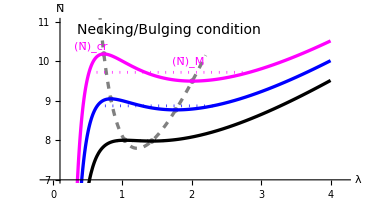

```mathematica
subfig3a=Plot[{FF[λ,γ1[[1]],0.2,0.2],FF[λ,γ1[[2]],0.2,0.2],FF[λ,γ1[[3]],0.2,0.2]},{λ,0,4},PlotStyle->{{Black, Thickness[0.0065]},{Blue,Thickness[0.0065]},{Magenta,Thickness[0.0065]}}];fig3a=Show[Plot[Ncr1[λ,0.2,0.2],{λ,0,2.2},PlotRange->{{0.4,2.2},{6,12}},PlotStyle->{{Gray,Dashed,Thickness[0.0065]}}],ListPlot[datacr1,PlotMarkers->"OpenMarkers",PlotStyle->Gray],subfig2a,PlotRange->{{-0.1,4.2},{7,11}},AxesOrigin->{0.1,7},Epilog->{Text[Style["(N̄)_cr",FontColor->Magenta],{0.55,10.36}],Text[Style["(N̄)_M",FontColor->Magenta],{1.95,10}],Text[Style["Necking/Bulging condition",FontSize->14,FontColor->Black,FontFamily->"Times New Roman"],{1.67,10.8}],Black,Dotted,Thickness[0.0055],Line[{{maxwpt10[[1+1,1]],maxwpt10[[1+1,2]]},{maxwpt11[[1+1,1]],maxwpt11[[1+1,2]]}}],Blue,Line[{{maxwpt10[[2+1,1]],maxwpt10[[2+1,2]]},{maxwpt11[[2+1,1]],maxwpt11[[2+1,2]]}}],Magenta,Line[{{maxwpt10[[3+1,1]],maxwpt10[[3+1,2]]},{maxwpt11[[3+1,1]],maxwpt11[[3+1,2]]}}]},AxesStyle->Directive[Black,Thickness[0.0035],Arrowheads[{0,0.03}]],AspectRatio->0.55,AxesLabel->{Style["λ",FontSize->16,FontColor->Black,FontFamily->"Times New Roman"],Style[OverBar[N],FontSize->16,FontColor->Black,FontFamily->"Times New Roman"]}]
```

### 2.2 Solution of the 1-D gradient model-Case of Fixed γ=8,9,10, μs=0.2,νs=0.2, increase NN from zero

#### 2.2.1 1d model coefficients

```mathematica
ζ=(λ^2 w'[λ])/(λ^3-1);
η= (λ^(1/2)w'[λ])/(λ^3-1)+(Γ1[λ^(-1/2),λ]-λ Γ12[λ^(-1/2),λ]+2 λ^(5/2)Γ22[λ^(-1/2),λ])/(A λ);(*Eqs. (4.12)*)
B[λ_,γ_,μs_,νs_]=(A^4((ζ^2-η^2)/(16 ζ λ^3)+(Γ2 [λ^(-1/2),λ])/(4 λ^4 A)))/(1/2 A^2)//Simplify;(*Eq. (4.17), scaled by 1/2 A^2*)
CC[λ_,γ_,μs_,νs_]=(A^3 (Γ2 [λ^(-1/2),λ] η)/(8 ζ λ^(3/2)))/(1/2 A^2)//Simplify;(*Eq. (4.18), scaled by 1/2 A^2*)
DB[λ_,γ_,μs_,νs_]=D[B[λ,γ,μs,νs],λ]//Simplify;
```

#### 2.2.2 Collect {λ0,NN} data when λ∞ decreases from λcr1 to λM1

after necking, NN decreases from Ncr1[λcr1[[i]], 0.2, 0.2] to maxwpt10[[i + 1, 2]], i=1,2,3 corresponding to γ=8,9,10

case 1 : γ = 8

```mathematica
dataN11={{λcr1[[1]],Ncr1[λcr1[[1]],0.2,0.2]}};dataamp11={{Ncr1[λcr1[[1]],0.2,0.2]/maxwpt11[[1+1,2]],0}};
nn=200;
λ0=λcr1[[1]];
Do[λ∞=λcr1[[1]]-k*(λcr1[[1]]-maxwpt10[[1+1,1]])/nn;
NN=FF[λ∞,γ1[[1]],0.2,0.2];
λ0=x/.FindRoot[Phihom[x,NN,γ1[[1]],0.2,0.2]==Phihom[λ∞,NN,γ1[[1]],0.2,0.2],{x,1.03λ0,λcr1[[1]],1.1maxwpt11[[1+1,1]]}]//Re;
dataN11=Append[dataN11,{λ0,NN}];dataamp11=Append[dataamp11,{NN/maxwpt11[[1+1,2]],(1/Sqrt[λ∞]-1/Sqrt[λ0])}],{k,1,nn}]
Clear[NN]
dataNu11a=Table[{x,FF[x,γ1[[1]],0.2,0.2]},{x,0.5,λcr1[[1]]-(λcr1[[1]]-0.5)/nn,(λcr1[[1]]-0.5)/nn}](*λ0=λ∞<λcr*);
dataN1d11=Join[dataNu11a,dataN11];dataamp1d11=dataamp11;
```

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 MachinePrecision 位的工作精度以满足这些容差.

General::stop: 在本次计算中，FindRoot::lstol 的进一步输出将被抑制.

case 2: γ=9

```mathematica
dataN12={{λcr1[[2]],Ncr1[λcr1[[2]],0.2,0.2]}};dataamp12={{Ncr1[λcr1[[2]],0.2,0.2]/maxwpt11[[2+1,2]],0}};
nn=200;
λ0=λcr1[[2]];
Do[λ∞=λcr1[[2]]-k*(λcr1[[2]]-maxwpt10[[2+1,1]])/nn;
NN=FF[λ∞,γ1[[2]],0.2,0.2];
λ0=x/.FindRoot[Phihom[x,NN,γ1[[2]],0.2,0.2]==Phihom[λ∞,NN,γ1[[2]],0.2,0.2],{x,1.03λ0,λcr1[[2]],1.1maxwpt11[[2+1,1]]}]//Re;
dataN12=Append[dataN12,{λ0,NN}];dataamp12=Append[dataamp12,{NN/maxwpt11[[2+1,2]],(1/Sqrt[λ∞]-1/Sqrt[λ0])}],{k,1,nn}]
dataNu12a=Table[{x,FF[x,γ1[[2]],0.2,0.2]},{x,0.25,λcr1[[2]]-(λcr1[[2]]-0.25)/nn,(λcr1[[2]]-0.25)/nn}](*λ0=λ∞<λcr*);dataNu12c=Table[{x,FF[x,γ1[[2]],0.2,0.2]},{x,maxwpt11[[2+1,1]],4,(λcr1[[2]]-0.25)/nn}](*λ0=λ∞>λM2*);
dataN1d12=Join[dataNu12a,dataN12];dataamp1d12=dataamp12;
```

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 MachinePrecision 位的工作精度以满足这些容差.

case 3: γ=10

```mathematica
dataN13={{λcr1[[3]],Ncr1[λcr1[[3]],0.2,0.2]}};dataamp13={{Ncr1[λcr1[[3]],0.2,0.2]/maxwpt11[[3+1,2]],0}};
nn=200;
λ0=λcr1[[3]];
Do[λ∞=λcr1[[3]]-k*(λcr1[[3]]-maxwpt10[[3+1,1]])/nn;
NN=FF[λ∞,γ1[[3]],0.2,0.2];
λ0=x/.FindRoot[Phihom[x,NN,γ1[[3]],0.2,0.2]==Phihom[λ∞,NN,γ1[[3]],0.2,0.2],{x,1.03λ0,λcr1[[3]],1.1maxwpt11[[3+1,1]]}]//Re;
dataN13=Append[dataN13,{λ0,NN}];dataamp13=Append[dataamp13,{NN/maxwpt11[[3+1,2]],(1/Sqrt[λ∞]-1/Sqrt[λ0])}],{k,1,nn}]
Clear[NN];
dataNu13a=Table[{x,FF[x,γ1[[3]],0.2,0.2]},{x,0.25,λcr1[[3]]-(λcr1[[3]]-0.25)/nn,(λcr1[[3]]-0.25)/nn}](*λ0=λ∞<λcr*);dataNu13c=Table[{x,FF[x,γ1[[3]],0.2,0.2]},{x,maxwpt11[[3+1,1]],4,(λcr1[[3]]-0.25)/nn}](*λ0=λ∞>λM2*);
dataN1d13=Join[dataNu13a,dataN13];dataamp1d13=dataamp13;
```

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 MachinePrecision 位的工作精度以满足这些容差.

General::stop: 在本次计算中，FindRoot::lstol 的进一步输出将被抑制.

plots the NN-λ0 responses and the necking amplitudes for the three cases

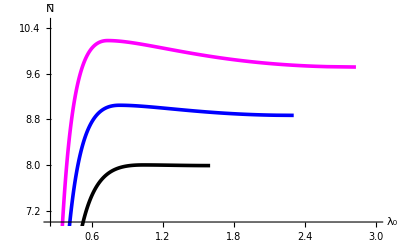

```mathematica
subfig3b=Show[ListLinePlot[{dataN1d11,dataN1d12,dataN1d13},PlotStyle->{{Black,Thickness[0.0065]},{Blue,Thickness[0.0065]},{Magenta,Thickness[0.0065]}}],AxesStyle->Directive[Black,Thickness[0.0035],Arrowheads[{0,0.03}]],AxesLabel->{Style["λ_0",FontSize->16,Black,FontFamily->"Times New Roman"],Style["N̄",FontSize->16,Black,FontFamily->"Times New Roman"]},PlotRange->{{0.25,3},{7,10.5}},AxesOrigin->{0.25,7}](*the solution of 1d model shown in Fig. 2(b)*)
```

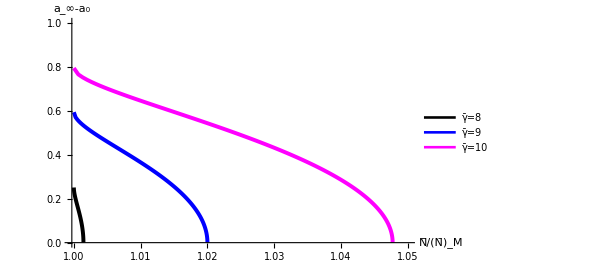

```mathematica
fig3c=ListLinePlot[{dataamp1d11,dataamp1d12,dataamp1d13},PlotStyle->{{Black,Thickness[0.0065]},{Blue,Thickness[0.0065]},{Magenta,Thickness[0.0065]}},PlotLegends->Placed[LineLegend[{Style["γ̄=8",14],Style["γ̄=9",14],Style["γ̄=10",14]},LegendMarkerSize->{25,5}, LegendLayout->{"Column",1}],{0.88,0.88}],AxesStyle->Directive[Black,Thickness[0.0035],Arrowheads[{0,0.03}]],AxesLabel->{Style["N̄/(N̄)_M",FontSize->16,FontColor->Black,FontFamily->"Times New Roman"],Style["a_∞-a_0",FontSize->16,FontColor->Black,FontFamily->"Times New Roman"]},PlotRange->{{0.9997,1.05},{0,1.}}](*the solution of 1d model shown in Fig. 2(b)*)
```

#### 2.2.3 Solutions for the evolutions of a[Z] in the cylinder by solving the 1d initial value problem

case 1: γ=8

```mathematica
L=40;aa1=Table[0,{i,1,4}];yy0=Table[0,{i,1,4}];f11[j_,r_]:=datacr1[[j,2]]-r(datacr1[[j,2]]-maxwpt10[[j+1,2]]);N11={f11[1,0.1],f11[1,0.5],f11[1,0.9],f11[1,0.9975]};
Do[N0=N11[[k]];γ11=γ1[[1]];
λ∞=x/.FindRoot[{FF[x,γ11,0.2,0.2]==N0},{x,0.9λcr1[[1]]}];
λ0=x/.FindRoot[ {Phihom[x,N0,γ11,0.2,0.2]==Phihom[λ∞,N0,γ11,0.2,0.2]},{x,1.λcr1[[1+3]]}];
yy0[[k]]=λ0;aa1[[k]]=Evaluate[y1[x]^(-1/2)/.NDSolve[{y1'[x]==y2[x],y2'[x]==Simplify[ 1/B[y1[x],γ11,0.2,0.2](DPhihom[y1[x],N0,γ11,0.2,0.2]-1/2 DB[y1[x],γ11,0.2,0.2] y2[x]^2)],y1[0]==λ0,y2[0]==0},{y1,y2},{x,0,L}]//First ],{k,1,4}]
point11=Table[{yy0[[k]],N11[[k]]},{k,1,4}]
```

{{1.13019,7.99966},{1.2922,7.99507},{1.47197,7.99047},{1.57859,7.98936}}

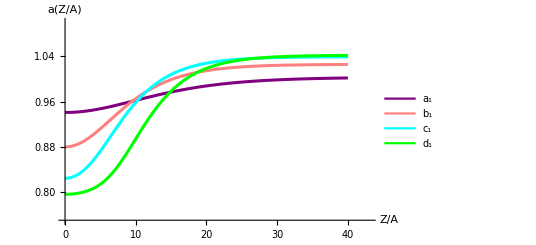

```mathematica
fig3a=Plot[{aa1[[1]],aa1[[2]],aa1[[3]],aa1[[4]]},{x,0,40},PlotStyle->{{Purple,Thickness[0.0055]},{Pink,Thickness[0.0055]},{Cyan,Thickness[0.0055]},{Green,Thickness[0.0055]}},PlotLegends->Placed[LineLegend[{Style["a_1",14],Style["b_1",14],Style["c_1",14],Style["d_1",14]},LegendMarkerSize->{25,5}, LegendLayout->{"Column",1}],{0.88,0.34}],PlotRange->{{0,43},{0.75,1.1}},AxesStyle->Directive[Black,Thickness[0.0035],Arrowheads[{0,0.03}]],AxesLabel->{Style["Z/A",FontSize->16,Black,FontFamily->"Times New Roman"],Style["a(Z/A)",FontSize->16,Black,FontFamily->"Times New Roman"]}](*Fig. 3(a) for γ=8*)
```

case 1: γ=9

{{1.02532,9.02993},{1.40369,8.95895},{1.90266,8.88797},{2.23956,8.87067}}

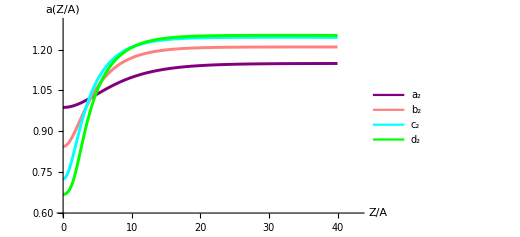

```mathematica
aa2=Table[0,{i,1,4}];yy0=Table[0,{i,1,4}];f11[i_,r_]:=datacr1[[i,2]]-r(datacr1[[i,2]]-maxwpt10[[i+1,2]]);N12={f11[2,0.1],f11[2,0.5],f11[2,0.9],f11[2,0.9975]};
Do[N0=N12[[k]];γ11=γ1[[2]];
λ∞=x/.FindRoot[{FF[x,γ11,0.2,0.2]==N0},{x,0.9λcr1[[2]]}];
λ0=x/.FindRoot[ {Phihom[x,N0,γ11,0.2,0.2]==Phihom[λ∞,N0,γ11,0.2,0.2]},{x,1.λcr1[[2+3]]}];
yy0[[k]]=λ0;aa2[[k]]=Evaluate[y1[x]^(-1/2)/.NDSolve[{y1'[x]==y2[x],y2'[x]==Simplify[ 1/B[y1[x],γ11,0.2,0.2](DPhihom[y1[x],N0,γ11,0.2,0.2]-1/2 DB[y1[x],γ11,0.2,0.2] y2[x]^2)],y1[0]==λ0,y2[0]==0},{y1,y2},{x,0,L}]//First ],{k,1,4}]
point12=Table[{yy0[[k]],N12[[k]]},{k,1,4}]
fig3b=Plot[{aa2[[1]],aa2[[2]],aa2[[3]],aa2[[4]]},{x,0,40},PlotStyle->{{Purple,Thickness[0.0055]},{Pink,Thickness[0.0055]},{Cyan,Thickness[0.0055]},{Green,Thickness[0.0055]}},PlotLegends->Placed[LineLegend[{Style["a_2",14],Style["b_2",14],Style["c_2",14],Style["d_2",14]},LegendMarkerSize->{25,5}, LegendLayout->{"Column",1}],{0.88,0.34}],PlotRange->{{0,43},{0.6,1.3}},AxesStyle->Directive[Black,Thickness[0.0035],Arrowheads[{0,0.03}]],AxesLabel->{Style["Z/A",FontSize->16,Black,FontFamily->"Times New Roman"],Style["a(Z/A)",FontSize->16,Black,FontFamily->"Times New Roman"]}](*Fig. 3(b) for γ=9*)
```

```mathematica
case 1: γ=10 . This case  is compared with the finite-element results
```

We solve the 1d model for  a(Z)=(λ(Z))^(-1/2) , z(Z)  and the Lagrange multiplier p(Z)=(λ(Z))^(-1/2)W3[(λ(Z))^(-1/2),λ(Z),(λ(Z))^(-1/2)]+Γ1[(λ(Z))^(-1/2),λ(Z)]/((λ(Z))^(-1/2) λ(Z) A) which enforces det (F) = 1. These 1d model solution will be set to initial values for the later finite-element scheme.

{{0.966401,10.1354},{1.46565,9.94985},{2.19468,9.76425},{2.72508,9.71901}}

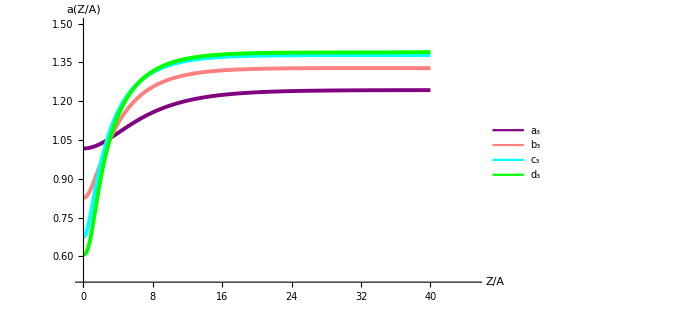

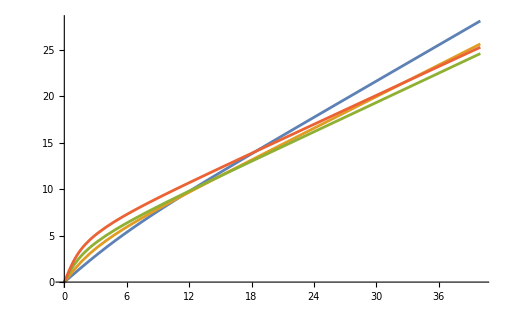

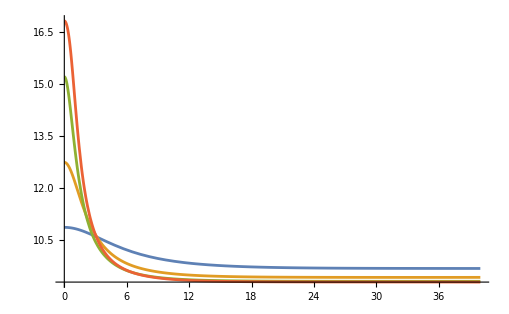

```mathematica
yy1d=Table[0,{i,1,4}];aa1d=Table[0,{i,1,4}];zz1d=Table[0,{i,1,4}];pp1d=Table[0,{i,1,4}];yy0=Table[0,{i,1,4}];f11[i_,r_]:=datacr1[[i,2]]-r(datacr1[[i,2]]-maxwpt10[[i+1,2]]);N13={f11[3,0.1],f11[3,0.5],f11[3,0.9],f11[3,0.9975]};
Do[N0=N13[[k]];γ11=γ1[[3]];
λ∞=x/.FindRoot[{FF[x,γ11,0.2,0.2]==N0},{x,0.9λcr1[[3]]}];
λ0=x/.FindRoot[ {Phihom[x,N0,γ11,0.2,0.2]==Phihom[λ∞,N0,γ11,0.2,0.2]},{x,1.λcr1[[3+3]]}];λsub=NDSolve[{y1'[x]==y2[x],y2'[x]==Simplify[ 1/B[y1[x],γ11,0.2,0.2](DPhihom[y1[x],N0,γ11,0.2,0.2]-1/2 DB[y1[x],γ11,0.2,0.2] y2[x]^2)],y1[0]==λ0,y2[0]==0},{y1,y2},{x,0,L}]//First;
yy0[[k]]=λ0;yy1d[[k]]=y1[x]/.λsub;aa1d[[k]]=y1[x]^(-1/2) /.λsub;zz1d[[k]]=Integrate[y1[x]/.λsub,x];(*position function z(Z), whose 1d solution will be used as the initial values in the 3d FE simulation*)pp1d[[k]]=y1[x]^(-1/2)W3[y1[x]^(-1/2),y1[x],y1[x]^(-1/2)]+Γ1[y1[x]^(-1/2),y1[x]]/(y1[x]^(-1/2) y1[x] A)/.γ->10/.μs->0.2/.νs->0.2/.λsub,{k,1,4}](*Lagrange multiplier enforcing det(F)=1, whose 1d solution will be used as the initial values in the 3d FE simulation*)
point13=Table[{yy0[[k]],N13[[k]]},{k,1,4}]
fig4c=Show[Plot[{aa1d[[1]],aa1d[[2]],aa1d[[3]],aa1d[[4]]},{x,0,40},PlotStyle->{{Purple,Thickness[0.0055]},{Pink,Thickness[0.0055]},{Cyan,Thickness[0.0055]},{Green,Thickness[0.0055]}},PlotLegends->Placed[LineLegend[{Style["a_3",14],Style["b_3",14],Style["c_3",14],Style["d_3",14]},LegendMarkerSize->{25,5}, LegendLayout->{"Column",1}],{0.88,0.34}],PlotRange->{{0,43},{0.5,1.5}},AxesStyle->Directive[Black,Thickness[0.0035],Arrowheads[{0,0.03}]],AxesLabel->{Style["Z/A",FontSize->16,Black,FontFamily->"Times New Roman"],Style["a(Z/A)",FontSize->16,Black,FontFamily->"Times New Roman"]}],PlotRange->{{0,45},{0.5,1.5}}](*solution of a(Z), Fig. 4(c) for γ=10*)
Plot[{zz1d[[1]],zz1d[[2]],zz1d[[3]],zz1d[[4]]},{x,0,40}](*solution of z(Z) γ=10*)
Plot[{pp1d[[1]],pp1d[[2]],pp1d[[3]],pp1d[[4]]},{x,0,40},PlotRange->All](*solution of p(Z) γ=10*)
```

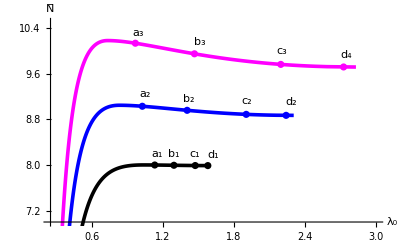

```mathematica
fig3b=Show[subfig3b,ListPlot[{point11,point12,point13},PlotStyle->{Black,Blue,Magenta}],Epilog->{Inset[Text[Style["a_1",16]],{1.15,8.20}],Inset[Text[Style["b_1",16]],{1.29,8.20}],Inset[Text[Style["c_1",16]],{1.47,8.2}],Inset[Text[Style["d_1",16]],{1.62,8.18}],Inset[Text[Style["a_2",16]],{1.05,9.24}],Inset[Text[Style["b_2",16]],{1.42,9.16}],Inset[Text[Style["c_2",16]],{1.91,9.12}],Inset[Text[Style["d_2",16]],{2.28,9.1}],Inset[Text[Style["a_3",16]],{0.99,10.32}],Inset[Text[Style["b_3",16]],{1.51,10.15}],Inset[Text[Style["c_3",16]],{2.2,10.00}],Inset[Text[Style["d_4",16]],{2.75,9.925}]},AxesStyle->Directive[Black,Thickness[0.0035],Arrowheads[{0,0.03}]],AxesLabel->{Style["λ_0",FontSize->16,Black,FontFamily->"Times New Roman"],Style["N̄",FontSize->16,Black,FontFamily->"Times New Roman"]},PlotRange->{{0.25,3},{7,10.5}},AxesOrigin->{0.25,7}](*add the four stage points to each curve in Fig. 2(b)*)
```

## 3. Finite-element solution for the 2D axisymmetric deformation-- computed using Rayleigh-Ritz method

#### 3.1 Bulk deformation gradient and surface deformation gradient

```mathematica
F=({{𝒶, 0, 0}, {0, zZ, zR}, {0, 𝒶Z R, 𝒶+𝒶R R}});(* introudce r=a R to avoid the singularlity at R=0*)
Fs=({{𝒶, 0, 0}, {0, zZ, 0}, {0, 𝒶Z A, 0}});(*surface deformation gradient*)
𝒞=Transpose[F].F;
𝒞s=Transpose[Fs].Fs;
I1=Tr[𝒞];
I1s=Tr[𝒞s];
J=Det[F];
Js=𝒶*(zZ^2+A^2 𝒶Z^2)^(1/2);(*determinant of surface deformation graident, computed by Js=√(det(Cs))*)
```

#### 3.2 Define shape functions, 4-node bilinear quadrilateral(Q4) elements for displacement u[x,y]≈a_1+a_2 x+a_3 y+a_4 x y=u_1 N_1[x,y]+u_2 N_2[x,y]+u_3 N_3[x,y]+u_4 N_4[x,y], constant elements for Lagrange multiplier p[x,y]≈a_1, use 4-point Gaussian quadrature rule

```mathematica
N1[x_,y_]=(x-1)(y-1);(* Shape function for node 1, we consider a standard square [0,1]x[0,1], the node are labeled according to [0,0]->1, [1,0]->2, [1,1]->3, [0,1]->4*)
N1x[x_,y_]=Derivative[1,0][N1][x,y];
N1y[x_,y_]=Derivative[0,1][N1][x,y];
N2[x_,y_]=x(1-y);
N2x[x_,y_]=Derivative[1,0][N2][x,y];
N2y[x_,y_]=Derivative[0,1][N2][x,y];
N3[x_,y_]=x y;
N3x[x_,y_]=Derivative[1,0][N3][x,y];
N3y[x_,y_]=Derivative[0,1][N3][x,y];
N4[x_,y_]=(1-x)y; 
N4x[x_,y_]=Derivative[1,0][N4][x,y];
N4y[x_,y_]=Derivative[0,1][N4][x,y];
({{N1[0,0], N1[1,0], N1[1,1], N1[0,1]}, {N2[0,0], N2[1,0], N2[1,1], N2[0,1]}, {N3[0,0], N3[1,0], N3[1,1], N3[0,1]}, {N4[0,0], N4[1,0], N4[1,1], N4[0,1]}})-DiagonalMatrix[{1,1,1,1}]//Simplify//MatrixForm
uintp[x_,y_]=u1 N1[x,y]+u2 N2[x,y]+u3 N3[x,y]+u4 N4[x,y];(*bilinerar interpolation of u[x,y]*)
{uintp[0,0],uintp[1,0],uintp[1,1],uintp[0,1]}
{x1,x2}={1/2(1-√(1/3)),1/2(1+√(1/3))}//N;(*Guass points*)
{y1,y2}={1/2(1-√(1/3)),1/2(1+√(1/3))}//N;
{w1,w2}={1/2,1/2}//N;
utest[x_,y_]=1+2 x +3 y +4x y+5 x^2+6 x y+7 y^2;
Integrate[utest[x,y],{x,0,1},{y,0,1}]-(w1^2 utest[x1,y1]+w2 w1 utest[x2,y1]+w1 w2 utest[x1,y2]+w2^2 utest[x2,y2])//Simplify (*test Gaussian quadrature*)
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

{u1,u2,u3,u4}

0.

#### 3.3 Interpolation rules according to subsection 3.2

```mathematica
sub={zZ->N1x[x,y] z[i,j]/h+N2x[x,y] (z [i+1,j])/h+N3x[x,y] z[i+1,j+1]/h+N4x[x,y] z[i,j+1]/h,zR->N1y[x,y] z[i,j]/h+N2y[x,y] (z [i+1,j])/h+N3y[x,y] z[i+1,j+1]/h+N4y[x,y] z[i,j+1]/h,𝒶Z->N1x[x,y] a[i,j]/h+N2x[x,y] (a [i+1,j])/h+N3x[x,y] a[i+1,j+1]/h+N4x[x,y] a[i,j+1]/h,𝒶R-> N1y[x,y] a[i,j]/h+N2y[x,y] (a [i+1,j])/h+N3y[x,y] a[i+1,j+1]/h+N4y[x,y] a[i,j+1]/h,𝒶->N1[x,y]a[i,j]+N2[x,y] a [i+1,j]+N3[x,y]a[i+1,j+1]+N4[x,y]a[i,j+1],𝓅->p[i,j],R->j h+ y h};
sub11=sub/.{x->x1,y->y1};
sub21=sub/.{x->x2,y->y1};
sub12=sub/.{x->x1,y->y2};
sub22=sub/.{x->x2,y->y2};
subs={zZ->N3x[x,1] z[i+1,m]/h+N4x[x,1] z[i,m]/h,𝒶Z->N3x[x,1] a[i+1,m]/h+N4x[x,1] a[i,m]/h,𝒶->N3[x,1]a[i+1,m]+N4[x,1]a[i,m]};
subs1=subs/.{x->x1};
subs2=subs/.{x->x2};
```

#### 3.4 Meshing: discretize the domain

R (1/2 (-3+zR^2+zZ^2+𝒶^2+(𝒶+R 𝒶R)^2+R^2 𝒶Z^2)-(-1+zZ 𝒶^2+R zZ 𝒶 𝒶R-R zR 𝒶 𝒶Z) 𝓅)

10 𝒶 √(zZ^2+𝒶Z^2)+0.1 (-2+zZ^2+𝒶^2+𝒶Z^2-2 Log[𝒶 √(zZ^2+𝒶Z^2)])+0.05 (1/2 (-1+𝒶^2 (zZ^2+𝒶Z^2))-Log[𝒶 √(zZ^2+𝒶Z^2)])

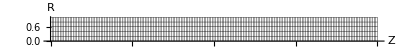

```mathematica
γ=10;νs=0.2;μs=0.2;(*Here only present the case of γ=10*)
int=(1/2(I1-3)-𝓅(J-1) )R
ints=A(γ Js+ μs/2(I1s-2-2 Log[Js])+λs/2(1/2(Js^2-1)-Log[Js]))
m=5;
n=L*m;
h=N[A/m];
ListPlot[Join[Table[{i*h,j*h},{j,0,m},{i,0,n}],Table[{i*h,j*h},{i,0,n},{j,0,m}]],Joined->True,AspectRatio->1/10,ImageSize->Full,PlotStyle->{{Black,Thickness->0.0007},{Black,Thickness->0.0007}},AxesLabel->{HoldForm[Z],HoldForm[R]}](*Draw the mesh*)
```

#### 3.5 Algebraic equations given by Rayleigh-Ritz approach

```mathematica
DateList[]
ℰ=Sum[w1^2(int/.sub11)+w2 w1(int/.sub21)+w1 w2(int/.sub12)+w2^2(int/.sub22),{j,0,m-1},{i,0,n-1}]+1/h Sum[w1(ints/.subs1)+w2(ints/.subs2),{i,0,n-1}]; (*discrete enerngy function*)
bcz0=Table[z[0,j]==0,{j,0,m}]; (*impose essential symmetric boundary conditions, z[0,R]==0*)
eqsz=Flatten[Table[D[ℰ,z[i,j]]==0,{j,0,m},{i,1,n-1}],1];
bczL=Table[z[n,j]-l==0,{j,0,m}];(*impose essential symmetric boundary conditions, Z[L,R]==l*)
eqsa=Flatten[Table[D[ℰ,a[i,j]]==0,{j,0,m},{i,0,n}],1];
eqsp=Flatten[Table[D[ℰ,p[i,j]]==0,{j,0,m-1},{i,0,n-1}],1];
eqN={h^2*Sum[D[ℰ,z[n,j]],{j,0,m}]-Nst*1/2 A^2==0};(*Nst means the axial force per unit area of the cross-section*)
eqs=Join[bcz0,eqsz,bczL,eqsa,eqsp,eqN];
DateList[]
eqs//Dimensions (*number of algebraic equations*)
```

{2024,11,22,20,49,41.5471171}

{2024,11,22,20,51,21.4307624}

{3413}

#### 3.6 Use 1 d model solutions given in subsubsection 2.2.3 as initial guess

```mathematica
Nstart=f11[3,0.1];NM=maxwpt10[[3+1,2]];Ncr=datacr1[[3,2]];
Nst=Nstart;
guessz=Flatten[Table[{z[i,j],N[zz1d[[1]]/.x->i h]},{j,0,m},{i,0,n}],1];
guessa=Flatten[Table[{a[i,j],N[aa1d[[1]]/.x->i h]},{j,0,m},{i,0,n}],1];
guessp=Flatten[Table[{p[i,j],N[pp1d[[1]]/.x->i h]},{j,0,m-1},{i,0,n-1}],1];
guesszL={{l,zz1d[[1]]/.x->L}};
guess=Join[guessz,guessa,guessp,guesszL];
guess//Dimensions
```

{3413,2}

#### 3.7 Find the finite-element solution

```mathematica
DateList[]
solsub=FindRoot[eqs,guess]
solsubini=solsub;(*store this solution*)
DateList[]
dataN={{(a[0,0]^-2+a[0,m]^-2)/2/.solsub,Nst}};
dataNλ={{l/L/.solsub,Nst}};
dataAmp={{Nst/NM,a[n,m]-a[0,m]}/.solsub};
datasol={solsub};
```

{2024,11,22,20,52,3.7291617}

{2024,11,22,20,52,16.355515}

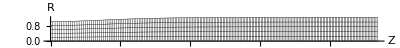

```mathematica
ListPlot[Join[Table[{z[i,j],a[i,j]*j h}/.solsub,{j,0,m},{i,0,n}],Table[{z[i,j],a[i,j]*j h}/.solsub,{i,0,n},{j,0,m}]],Joined->True,AspectRatio->1/10,ImageSize->Full,PlotStyle->{{Black,Thickness->0.0007},{Black,Thickness->0.0007}},AxesLabel->{HoldForm[Z],HoldForm[R]}](*mesh after deformation*)
```

#### 3.8 Compare with the 1d model solutions for a(Z), z(Z) and p(Z)

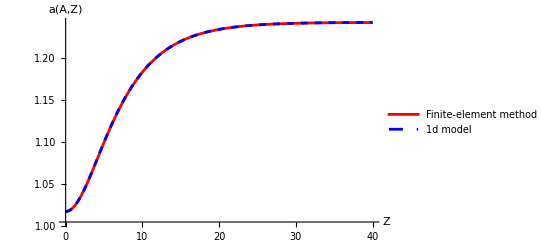

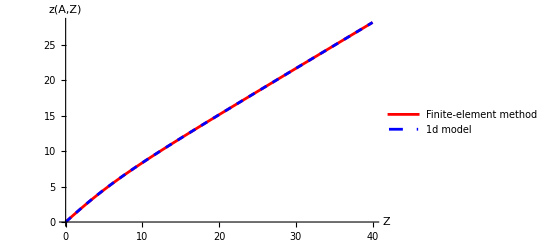

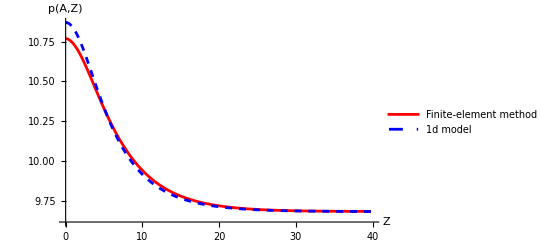

```mathematica
ListPlot[{Table[{i h,a[i,m ]/.solsub},{i,0,n}],Table[{i h,aa1d[[1]]/.x->i h},{i,0,n}]},Joined->True,PlotRange->Full,Joined->True,PlotRange->Full,AxesLabel->{HoldForm[Z],HoldForm[a[A,Z]]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]},PlotStyle->{{Red,Full},{Blue,Dashed}},PlotLegends->{"Finite-element method","1d model"}](*Compare the solutions for a(Z)*)
ListPlot[{Table[{i h,z[i,m ]/.solsub},{i,0,n}],Table[{i h,zz1d[[1]]/.x->i h},{i,0,n}]},Joined->True,PlotRange->Full,Joined->True,PlotRange->Full,AxesLabel->{HoldForm[Z],HoldForm[z[A,Z]]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]},PlotStyle->{{Red,Full},{Blue,Dashed}},PlotLegends->{"Finite-element method","1d model"}](*Compare the solutions for z(Z)*)
ListPlot[{Table[{i h,p[i,m-1 ]/.solsub},{i,0,n}],Table[{i h,pp1d[[1]]/.x->i h},{i,0,n}]},Joined->True,PlotRange->Full,Joined->True,PlotRange->Full,AxesLabel->{HoldForm[Z],HoldForm[p[A,Z]]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]},PlotStyle->{{Red,Full},{Blue,Dashed}},PlotLegends->{"Finite-element method","1d model"}](*Compare the solutions for p(Z)*)
```

#### 3.9 Find solutions when N varies, so as to trace the bifurcation

```mathematica
DateList[]
kmax=100;NM=maxwpt10[[3+1,2]];Ncr=datacr1[[3,2]];
Do[Nst=Nstart-k*(Nstart-NM)/kmax;
guessz=Flatten[Table[{z[i,j],z[i,j]/.solsub},{j,0,m},{i,0,n}],1];
guessa=Flatten[Table[{a[i,j],a[i,j]/.solsub},{j,0,m},{i,0,n}],1];
guessp=Flatten[Table[{p[i,j],p[i,j]/.solsub},{j,0,m-1},{i,0,n-1}],1];
guesszL={{l,l/.solsub}};
guess=Join[guessz,guessa,guessp,guesszL];
solsub=FindRoot[eqs,guess];
dataN=Append[dataN,{((a[0,0]^-2+a[0,m]^-2)/2)/.solsub,Nst}];dataNλ=Append[dataNλ,{l/L/.solsub,Nst}];
dataAmp=Append[dataAmp,{Nst/NM,a[n,m]-a[0,m]}/.solsub];
datasol=Append[datasol,solsub];Print[{k,Nst,(a[0,0]^-2+a[0,m]^-2)/2,l/L,a[n,m]-a[0,m]}/.solsub],{k,1,kmax}](*N descreases from Nstart*)
solsub=solsubini;
kmax2=40;
Do[Nst=Nstart+k*(Ncr-Nstart)/kmax2;
guessz=Flatten[Table[{z[i,j],z[i,j]/.solsub},{j,0,m},{i,0,n}],1];
guessa=Flatten[Table[{a[i,j],a[i,j]/.solsub},{j,0,m},{i,0,n}],1];
guessp=Flatten[Table[{p[i,j],p[i,j]/.solsub},{j,0,m-1},{i,0,n-1}],1];
guesszL={{l,l/.solsub}};
guess=Join[guessz,guessa,guessp,guesszL];
solsub=FindRoot[eqs,guess];
dataN=Prepend[dataN,{(a[0,0]^-2+a[0,m]^-2)/2/.solsub,Nst}];dataNλ=Prepend[dataNλ,{l/L/.solsub,Nst}];
dataAmp=Prepend[dataAmp,{Nst/NM,a[n,m]-a[0,m]}/.solsub];
datasol=Prepend[datasol,solsub];Print[{k,Nst,(a[0,0]^-2+a[0,m]^-2)/2,l/L,a[n,m]-a[0,m]}/.solsub],{k,1,kmax2}](*N increases from Nstart*)
DateList[]
dataN;
dataAmp;
datasol;
```

{2024,7,31,12,19,59.5073917}

{1,10.1313,0.981252,0.700406,0.234985}

{2,10.1271,0.993868,0.698147,0.244368}

{3,10.1229,1.00625,0.695976,0.253392}

{4,10.1187,1.01843,0.693885,0.262094}

{5,10.1146,1.03044,0.691866,0.270507}

{6,10.1104,1.04229,0.689913,0.278659}

{7,10.1062,1.05402,0.688022,0.286574}

{8,10.102,1.06562,0.686188,0.294271}

{9,10.0979,1.07713,0.684408,0.301768}

{10,10.0937,1.08854,0.682676,0.30908}

{11,10.0895,1.09988,0.680991,0.316222}

{12,10.0853,1.11116,0.67935,0.323206}

{13,10.0812,1.12237,0.67775,0.330041}

{14,10.077,1.13354,0.676189,0.336738}

{15,10.0728,1.14467,0.674664,0.343305}

{16,10.0686,1.15577,0.673175,0.349751}

{17,10.0645,1.16684,0.671718,0.356083}

{18,10.0603,1.17788,0.670294,0.362306}

{19,10.0561,1.18892,0.668899,0.368428}

{20,10.0519,1.19994,0.667533,0.374454}

{21,10.0478,1.21097,0.666195,0.380388}

{22,10.0436,1.22199,0.664883,0.386235}

{23,10.0394,1.23302,0.663597,0.392001}

{24,10.0352,1.24406,0.662335,0.397688}

{25,10.031,1.25511,0.661097,0.403301}

{26,10.0269,1.26618,0.659882,0.408844}

{27,10.0227,1.27728,0.658688,0.414319}

{28,10.0185,1.2884,0.657516,0.419729}

{29,10.0143,1.29955,0.656364,0.425078}

{30,10.0102,1.31073,0.655231,0.430368}

{31,10.006,1.32196,0.654118,0.435602}

{32,10.0018,1.33322,0.653024,0.440783}

{33,9.99764,1.34453,0.651948,0.445912}

{34,9.99346,1.35588,0.650889,0.450992}

{35,9.98929,1.36729,0.649848,0.456025}

{36,9.98511,1.37875,0.648823,0.461013}

{37,9.98094,1.39027,0.647815,0.465959}

{38,9.97676,1.40185,0.646823,0.470862}

{39,9.97258,1.4135,0.645846,0.475727}

{40,9.96841,1.42521,0.644884,0.480554}

{41,9.96423,1.437,0.643937,0.485344}

{42,9.96006,1.44886,0.643005,0.490101}

{43,9.95588,1.46081,0.642087,0.494824}

{44,9.9517,1.47283,0.641184,0.499515}

{45,9.94753,1.48495,0.640294,0.504177}

{46,9.94335,1.49715,0.639417,0.50881}

{47,9.93918,1.50945,0.638554,0.513416}

{48,9.935,1.52185,0.637704,0.517995}

{49,9.93083,1.53436,0.636868,0.52255}

{50,9.92665,1.54697,0.636044,0.527082}

{51,9.92247,1.55969,0.635232,0.531592}

{52,9.9183,1.57253,0.634434,0.53608}

{53,9.91412,1.5855,0.633648,0.540549}

{54,9.90995,1.59859,0.632874,0.545}

{55,9.90577,1.61181,0.632113,0.549434}

{56,9.90159,1.62517,0.631363,0.553851}

{57,9.89742,1.63868,0.630626,0.558254}

{58,9.89324,1.65234,0.629902,0.562644}

{59,9.88907,1.66615,0.629189,0.567021}

{60,9.88489,1.68013,0.628489,0.571387}

{61,9.88071,1.69428,0.627801,0.575743}

{62,9.87654,1.70861,0.627125,0.580091}

{63,9.87236,1.72312,0.626461,0.584432}

{64,9.86819,1.73783,0.62581,0.588767}

{65,9.86401,1.75274,0.625172,0.593097}

{66,9.85984,1.76787,0.624546,0.597424}

{67,9.85566,1.78322,0.623933,0.60175}

{68,9.85148,1.7988,0.623333,0.606076}

{69,9.84731,1.81463,0.622747,0.610403}

{70,9.84313,1.83072,0.622174,0.614734}

{71,9.83896,1.84709,0.621615,0.61907}

{72,9.83478,1.86374,0.621071,0.623412}

{73,9.8306,1.8807,0.620541,0.627764}

{74,9.82643,1.89798,0.620027,0.632126}

{75,9.82225,1.9156,0.619529,0.636502}

{76,9.81808,1.93359,0.619047,0.640894}

{77,9.8139,1.95196,0.618583,0.645304}

{78,9.80972,1.97074,0.618137,0.649736}

{79,9.80555,1.98996,0.61771,0.654192}

{80,9.80137,2.00966,0.617303,0.658676}

{81,9.7972,2.02986,0.616919,0.663192}

{82,9.79302,2.05061,0.616557,0.667745}

{83,9.78884,2.07196,0.616221,0.672339}

{84,9.78467,2.09395,0.615912,0.67698}

{85,9.78049,2.11665,0.615633,0.681674}

{86,9.77632,2.14013,0.615387,0.686429}

{87,9.77214,2.16447,0.615178,0.691254}

{88,9.76797,2.18976,0.61501,0.696159}

{89,9.76379,2.21614,0.61489,0.701157}

{90,9.75961,2.24374,0.614824,0.706262}

{91,9.75544,2.27274,0.614823,0.711495}

{92,9.75126,2.30337,0.614898,0.716878}

{93,9.74709,2.33594,0.615068,0.722444}

{94,9.74291,2.37085,0.615356,0.728236}

{95,9.73873,2.40867,0.6158,0.734315}

{96,9.73456,2.45026,0.616457,0.740773}

{97,9.73038,2.49702,0.61743,0.747759}

{98,9.72621,2.55149,0.618921,0.755552}

{99,9.72203,2.61961,0.621461,0.764803}

{100,9.71785,2.72681,0.627851,0.77839}

{1,10.1366,0.96473,0.703434,0.222395}

{2,10.1378,0.961071,0.704115,0.219559}

{3,10.1389,0.957384,0.704806,0.216683}

{4,10.1401,0.95367,0.705505,0.213767}

{5,10.1412,0.949926,0.706215,0.210809}

{6,10.1424,0.94615,0.706934,0.207807}

{7,10.1436,0.942342,0.707663,0.204758}

{8,10.1447,0.9385,0.708403,0.201662}

{9,10.1459,0.934621,0.709154,0.198514}

{10,10.147,0.930705,0.709917,0.195314}

{11,10.1482,0.926747,0.710692,0.192057}

{12,10.1494,0.922747,0.711479,0.188742}

{13,10.1505,0.918701,0.712279,0.185364}

{14,10.1517,0.914607,0.713093,0.18192}

{15,10.1528,0.910462,0.713922,0.178406}

{16,10.154,0.906261,0.714765,0.174818}

{17,10.1552,0.902002,0.715625,0.171151}

{18,10.1563,0.89768,0.716501,0.167399}

{19,10.1575,0.89329,0.717395,0.163556}

{20,10.1586,0.888828,0.718307,0.159616}

{21,10.1598,0.884286,0.719239,0.15557}

{22,10.161,0.879659,0.720192,0.15141}

{23,10.1621,0.874938,0.721167,0.147127}

{24,10.1633,0.870115,0.722167,0.142707}

{25,10.1644,0.86518,0.723192,0.138138}

{26,10.1656,0.860119,0.724244,0.133403}

{27,10.1668,0.85492,0.725326,0.128483}

{28,10.1679,0.849564,0.726441,0.123356}

{29,10.1691,0.844031,0.727591,0.117993}

{30,10.1702,0.838295,0.72878,0.112359}

{31,10.1714,0.832322,0.730012,0.106409}

{32,10.1726,0.826072,0.731291,0.100083}

{33,10.1737,0.819486,0.732624,0.0933032}

{34,10.1749,0.812486,0.734018,0.0859568}

{35,10.176,0.804956,0.735483,0.0778776}

{36,10.1772,0.796712,0.73703,0.068798}

{37,10.1784,0.787432,0.738676,0.0582365}

{38,10.1795,0.776417,0.740443,0.0451355}

{39,10.1807,0.76128,0.742364,0.0258115}

FindRoot::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

{40,10.1818,0.748272,0.743277,0.00748761}

{2024,7,31,12,52,47.9711156}

#### 3.10 Comparison with 1 d model solutions for NN-λ0 response and necking amplitude

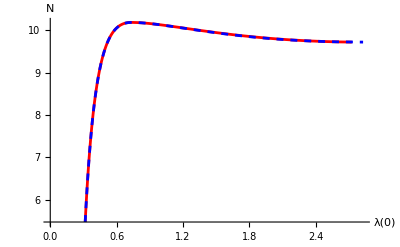

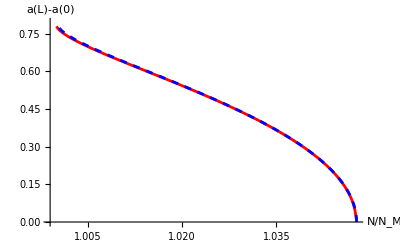

```mathematica
ListPlot[{Join[dataNu13a,dataN],dataN1d13},Joined->True,AxesLabel->{HoldForm[λ[0]],HoldForm[N]},PlotStyle->{{Red,Full},{Blue,Dashed}}]
ListPlot[{dataAmp,dataamp1d13},Joined->True,AxesLabel->{HoldForm[N/Subscript[N, M]],HoldForm[a[L]-a[0]]},PlotStyle->{{Red,Full},{Blue,Dashed}}]
```

#### 3.11 Show the Necking shape evolutions

```mathematica
m=5;h=1/5;n=40/h;ListPlot[Join[Table[{i*h,j*h},{j,0,m},{i,0,n}],Table[{i*h,j*h},{i,0,n},{j,0,m}]],Joined->True,AspectRatio->1/20,ImageSize->Full,PlotStyle->{{Black,Thickness->0.0007},{Black,Thickness->0.0007}},AxesLabel->{Style["Z"],Style["R"]}](*Draw the mesh in the reference configuration*)
```

-Graphics-

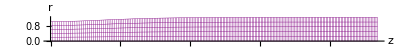

```mathematica
klist={41,85,41+89,41+100};rz1=Join[Table[{z[i,j],a[i,j]*j h}/.datasol[[klist[[1]]]],{j,0,m},{i,0,n}],Table[{z[i,j],a[i,j]*j h}/.datasol[[klist[[1]]]],{i,0,n},{j,0,m}]];ListPlot[rz1,Joined->True,AspectRatio->1/20,ImageSize->Full,PlotStyle->{{Purple,Thickness->0.0007},{Purple,Thickness->0.0007}},AxesLabel->{Style["z"],Style["r"]}](*Draw the mesh in stage 1*)
```

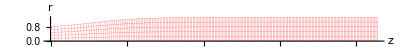

```mathematica
rz2=Join[Table[{z[i,j],a[i,j]*j h}/.datasol[[klist[[2]]]],{j,0,m},{i,0,n}],Table[{z[i,j],a[i,j]*j h}/.datasol[[klist[[2]]]],{i,0,n},{j,0,m}]];ListPlot[rz2,Joined->True,AspectRatio->1/20,ImageSize->Full,PlotStyle->{{Pink,Thickness->0.0007},{Pink,Thickness->0.0007}},AxesLabel->{Style["z"],Style["r"]}](*Draw the mesh in stage 2*)
```

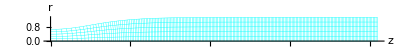

```mathematica
rz3=Join[Table[{z[i,j],a[i,j]*j h}/.datasol[[klist[[3]]]],{j,0,m},{i,0,n}],Table[{z[i,j],a[i,j]*j h}/.datasol[[klist[[3]]]],{i,0,n},{j,0,m}]];ListPlot[rz3,Joined->True,AspectRatio->1/20,ImageSize->Full,PlotStyle->{{Cyan,Thickness->0.0007},{Cyan,Thickness->0.0007}},AxesLabel->{Style["z"],Style["r"]}](*Draw the mesh in stage 3*)
```

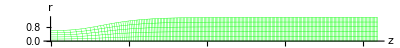

```mathematica
rz4=Join[Table[{z[i,j],a[i,j]*j h}/.datasol[[klist[[4]]]],{j,0,m},{i,0,n}],Table[{z[i,j],a[i,j]*j h}/.datasol[[klist[[4]]]],{i,0,n},{j,0,m}]];ListPlot[rz4,Joined->True,AspectRatio->1/20,ImageSize->Full,PlotStyle->{{Green,Thickness->0.0007},{Green,Thickness->0.0007}},AxesLabel->{Style["z"],Style["r"]}](*Draw the mesh in stage 4*)
```